# Twin-peak QPO relations in the Hartle-Thorne metric

This Mathematica notebook serves as supplementary material to the paper by Török et al. (submitted to MNRAS) and contains analytical relations used for modelling twin-peak quasi-periodic oscillations (QPOs) in the framework of the Hartle–Thorne spacetime.

The notebook provides the metric coefficients of the Hartle–Thorne solution, expressions for the Keplerian orbital frequency, radial and vertical epicyclic frequencies, and calculations of the innermost stable circular orbit (ISCO), following the formulation presented by Abramowicz et al. (2003). For modelling twin-peak QPOs, we use the approximate relations derived by Matuszková et al. (2024).

References
Hartle J. B. & Thorne K. S., 1968, APJ, 153, 807
Abramowicz M . A ., Almergren G . J . E ., Kluźniak W ., & Thampan A . V ., 2003, gr qc, gr - qc/0312070
Matuszková M., Török G., Klimovičová K., Horák J., Straub O., Šrámková E., Lančová D., Urbanec M., Urbancová G., Karas V., 2024, A&A, 691, A168

## The Hartle-Thorne metric coefficients

Equations (2) - (10) of Abramowicz et al. (2003) (with the misprint in equation (3) corrected)

```mathematica
F1=-(8M r^4 (r-2M))^(-1)(u^2(48M^6-8M^5r-24M^4r^2-30M^3r^3-60M^2r^4+135M r^5-45r^6)+(r-M)(16M^5+8M^4r-10M^2r^3-30M r^4+15r^5))+A1;
F2=(8M r(r-2M))^(-1)5(3u^2-1)(r-M)(2M^2+6M r-3r^2)-A1;
G1=(8M r^4 (r-2M))^(-1)(L-72M^5r-3u^2(L-56M^5r))-A1;
L=80M^6+8M^4r^2+10M^3r^3+20M^2r^4-45M r^5+15r^6;
H1=(8M r^4)^(-1)(1-3u^2)(16M^5+8M^4r-10M^2r^3+15M r^4+15r^5)+A2;
H2=(8M r)^(-1)5(1-3u^2)(2M^2-3M r-3r^2)-A2;
A1=15r(r-2M)(1-3u^2)/(16M^2) Log[r/(r-2M)];
A2 =15(r^2-2M^2)(3u^2-1)/(16M^2) Log[r/(r-2M)];
u = Cos[h];

metric=Array[g,{4,4}];
g[1,1]=-(1-2M/r)(1+j^2F1+q F2); g[1,2]=0; g[1,3]=0; g[1,4]=-2M^2/r j  (1-u^2);
g[2,1]=0; g[2,2]=(1-2M/r)^(-1)(1+j^2G1-q F2); g[2,3]=0; g[2,4]=0;
g[3,1]=0; g[3,2]=0; g[3,3]=r^2(1+j^2H1+q H2); g[3,4]=0;
g[4,1]=g[1,4]; g[4,2]=0; g[4,3]=0; g[4,4]=r^2(1-u^2)(1+j^2H1+q H2);
```

## The orbital angular velocity

Equations (16) - (20) of Abramowicz et al. (2003)

```mathematica
F1om=(48M^7-80M^6r+4M^5r^2-18M^4r^3+40M^3r^4+10M^2r^5+15M r^6-15r^7)(16M^2r^4(r-2M))^(-1)+Aom;
F2om=(5(6M^4-8M^3r-2M^2r^2-3M r^3+3r^4)/(16M^2r(r-2M)))-Aom;
Aom=(15(r^3-2M^3)/(32M^3))Log[r/(r-2M)];
ΩK=(M^(1/2)/r^(3/2))(1-j(M^(3/2)/r^(3/2))+j^2 F1om+q F2om);
```

## The radial epicyclic frequency

Equations (36), (38) - (41) of Abramowicz et al. (2003)

```mathematica
F1r=((6M^(3/2)(r+2M))/(r^(3/2)(r-6M)));
F2r=(8M^2r^4(r-2M)(r-6M))^(-1)(384M^8-720M^7r-112M^6r^2-76M^5r^3-138M^4r^4-130M^3r^5+635M^2r^6-375M r^7+60r^8)+Ar;
F3r=((5(48M^5+30M^4r+26M^3r^2-127M^2r^3+75M r^4-12r^5))/(8M^2r(r-2M)(r-6M)))-Ar;
Ar=((15r(r-2M)(2M^2+13M r-4r^2))/(16M^3(r-6M)))Log[r/(r-2M)];
ΩR=Sqrt[M(r-6M)r^(-4)(1+j F1r-j^2 F2r -q F3r)];
```

## The vertical epicyclic frequency

Equations (37), (42) - (45) of Abramowicz et al. (2003)

```mathematica
G1v=6M^(3/2)/r^(3/2);
G2v=(8M^2r^4(r-2M))^(-1)(48M^7-224M^6r+28M^5r^2+6M^4r^3-170M^3r^4+295M^2r^5-165M r^6+30r^7)-Bv;
G3v=5(6M^4+34M^3r-59M^2r^2+33M r^3-6r^4)/(8M^2r(r-2M))+Bv;
Bv=15(2r-M)(r-2M)^2/(16M^3)Log[r/(r-2M)];
Ωθ=Sqrt[M r^(-3)(1-j G1v+j^2 G2v +q G3v)];
```

## The innermost stable circular orbit

Equation (34) of Abramowicz et al. (2003)

```mathematica
rms=6M(1-j((2/3)Sqrt[2/3])+j^2((251647/2592)-240Log[3/2])+q((-9325/96)+240Log[3/2]));
```

Numerical calculation from Ω_R = 0

```mathematica
numrms:=r/.FindRoot[ΩR^2==0,{r,rms},AccuracyGoal->5]
```

## Unit conversion

Definitions of the speed of light, the gravitational constant, and the mass of the Sun

```mathematica
c=2.99792458 10^8; G=6.67428 10^-11; Msun=1.98892 10^30;
```

```mathematica
νK=ΩK c/(2Pi )/.r->r M/.M->G M Msun/c^2;
νR=ΩR c/(2Pi )/.r->r M/.M->G M Msun/c^2;
νθ=Ωθ c/(2Pi )/.r->r M/.M->G M Msun/c^2;
```

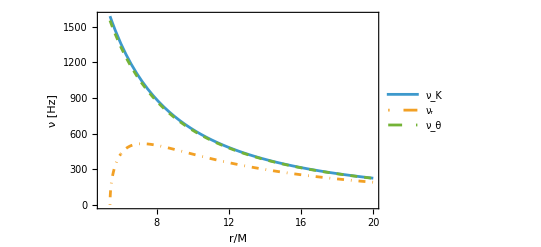

```mathematica
j=0.25; q=3.5j^2; M=1.6;r0=numrms;
Plot[{νK,νR,νθ},{r,r0/M,20},Frame->True,Axes->False,PlotRange->{{Floor[r0/M],20},{0,Automatic}},PlotStyle->{Line, DotDashed,Dashed},FrameLabel->{"r/M","ν [Hz]"},LabelStyle->Directive[20,FontFamily->"Times New Roman"],PlotLegends->{Subscript["ν","K"],Subscript["ν","r"],Subscript["ν","θ"]}]
Clear[j,q,M,r0]
```

## Relativistic Precession (RP) model

```mathematica
νP=νK-νR;
```

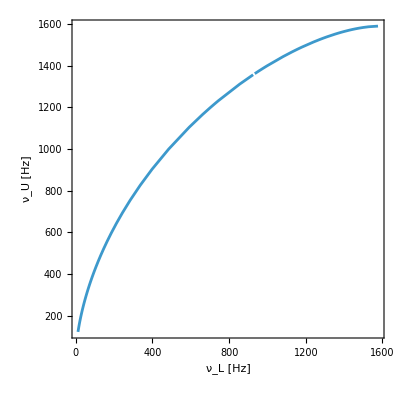

```mathematica
j=0.25;q=3.5j^2;M=1.6;r0=numrms;
ParametricPlot[{νP,νK},{r,r0/M,30},AspectRatio->1,PlotRange->Full,FrameLabel->{Row[{Subscript["ν","L"]," [Hz]"}],Row[{Subscript["ν","U"]," [Hz]"}]},LabelStyle->Directive[20,FontFamily->"Times New Roman"],Frame->True]
Clear[j,q,M,r0]
```

## Cusp Torus (CT) model

The full expressions for the radial precession frequency of a cusp torus are too lengthy to be included here; therefore, we use the approximate relations derived by Matuszková et al. (2024), while the complete implementation can be found in the accompanying Wolfram Mathematica notebook available at https://github.com/Astrocomp/HTtori_oscillations.

## Approximate twin-peak QPO relations

Equation (30), (36)  and (38) of Matuszková et al. (2024)

```mathematica
νL=νU(1-B Sqrt[1-6V0^(2/3)+8j V0+57j^2V0^(7/3)-3q V0^(4/3)(1+19V0)]); V0=νU/ν0/(6^1.5-j νU/ν0-1/2(j^2-q)(νU/ν0)^2); ν0=1/(2Pi)c^3/(G M Msun)/6^(3/2); B=1-0.2(1+j)bb^2;
(* bb = 0 -- RP model,   bb = 1 -- CT model *)
```

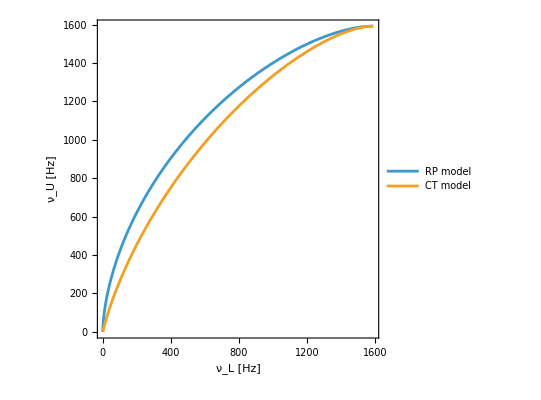

```mathematica
j=0.25;q=3.5j^2;M=1.6;
ParametricPlot[{{νL/.bb->0,νU},{νL/.bb->1,νU}},{νU,0,2000},AspectRatio->1,PlotRange->{{0,Automatic},{0,Automatic}},FrameLabel->{Row[{Subscript["ν","L"]," [Hz]"}],Row[{Subscript["ν","U"]," [Hz]"}]},LabelStyle->Directive[20,FontFamily->"Times New Roman"],PlotLegends->{"RP model","CT model"},Frame->True]
Clear[j,q,M]
```